# Circunferencias centradas en -1/3

```mathematica
z[x_]:=2/3(Cos[x]+I*Sin[x])-1/3
z1[x_,a_]:=a(Cos[x]+I*Sin[x])-1/3
```

# Método de Newton

```mathematica
F[z_]=(z+1/z)(1/2)
```

1/2 (1/z+z)

# Dibujos circunferencia e imágenes de las circunferencias por Newton y Schröeder

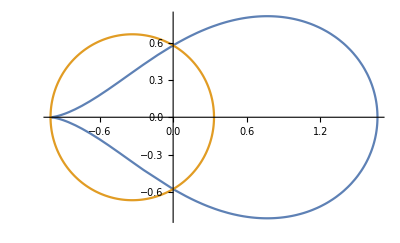

```mathematica
ParametricPlot[{{ReIm[F[z[x]]]},{ReIm[z[x]]}},{x,0,2Pi}]
```

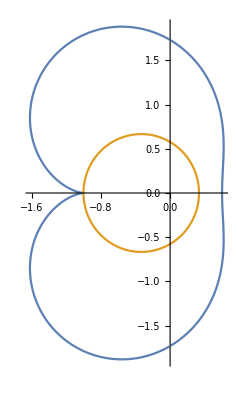

```mathematica
ParametricPlot[{{ReIm[1/(F[z[x]])]},{ReIm[z[x]]}},{x,0,2Pi}]
```

```mathematica
Animate[ParametricPlot[{{ReIm[F[z1[x,a]]]},{ReIm[z1[x,a]]}},{x,0,2Pi}],{a,0,5}]
```

```mathematica
Animate[ParametricPlot[{{ReIm[1/(F[z1[x,a]])]},{ReIm[z1[x,a]]}},{x,0,2Pi}],{a,0,5}]
```